```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes"]
```

C:\Users\pglpm\repositories\genobayes

```mathematica
NS["study_dirichlet_type_iii_2"]
```

```mathematica
assu=(aa>0&&nx>0&&t>0&&f1>0&&f2>0&&f3>0)
```

aa>0&&nx>0&&t>0&&f1>0&&f2>0&&f3>0

```mathematica
ClearAll[dirich];dirich[aa_,nx_,f_,t_]:=FS[(Multinomial@@(nx*f))*Gamma[aa]/Gamma[nx+aa]*(Times@@Gamma[nx*f+aa/t])/Gamma[aa/t]^t]
```

```mathematica
Assuming[assu,FS@D[dirich[aa,nx,{f1,f2,f3},t],aa]]
```

1/(t Gamma[aa+nx])Gamma[aa] Gamma[f1 nx+aa/t] Gamma[f2 nx+aa/t] Gamma[f3 nx+aa/t] Gamma[aa/t]^-t Multinomial[f1 nx,f2 nx,f3 nx] (t PolyGamma[0,aa]+PolyGamma[0,f1 nx+aa/t]+PolyGamma[0,f2 nx+aa/t]+PolyGamma[0,f3 nx+aa/t]-t (PolyGamma[0,aa+nx]+PolyGamma[0,aa/t]))

```mathematica
Assuming[assu&&%==0,FS@D[dirich[aa,nx,{f1,f2,f3},t],{aa,2}]]
```

1/(t^2 Gamma[aa+nx])Gamma[aa] Gamma[f1 nx+aa/t] Gamma[f2 nx+aa/t] Gamma[f3 nx+aa/t] Gamma[aa/t]^-t Multinomial[f1 nx,f2 nx,f3 nx] (t^2 PolyGamma[1,aa]+PolyGamma[1,f1 nx+aa/t]+PolyGamma[1,f2 nx+aa/t]+PolyGamma[1,f3 nx+aa/t]-t (t PolyGamma[1,aa+nx]+PolyGamma[1,aa/t]))

```mathematica
nn=5*10^6;
```

```mathematica
data=Import["scripts\\dataset1_simple.csv"];
n=Length[data[[;;,1]]];
Dimensions[data]
```

{6029,97}

```mathematica
ClearAll[fs];fs[ng_]:=fs[ng]=
SortBy[Tally[data[[;;,Join[{1,2,3},ng]]]],FromDigits[#[[1]],2]&][[;;,2]]/n
```

```mathematica
fs[Range[4]]
```

{1839/6029,588/6029,303/6029,93/6029,841/6029,261/6029,340/6029,103/6029,454/6029,173/6029,50/6029,23/6029,317/6029,111/6029,393/6029,140/6029}

```mathematica
ddir[aa_,nx_,f_]:=Block[{t=Length[f],n2=nx+aa,f2},
(Multinomial@@(nx*f))*Gamma[aa]/Gamma[n2]*(Times@@Gamma[nx*f+aa/t])/Gamma[aa/t]^t]
```

```mathematica
ClearAll[lddir1,lddir2];(*lddir1[nx_,f_]:=lddir1[nx,f]=Function[aa,D[Log[ddir[aa,nx,f]],aa]];
lddir2[nx_,f_]:=lddir2[nx,f]=Function[aa,D[Log[ddir[aa,nx,f]],{aa,2}]];*)
lddir1[aa_,nx_,f_]:=lddir1[aa,nx,f]=(D[Log[ddir[axx,nx,f]],axx]/.(axx->aa));
lddir2[aa_,nx_,f_]:=lddir2[aa,nx,f]=(D[Log[ddir[axx,nx,f]],{axx,2}]/.(axx->aa));
```

```mathematica
ClearAll[gau,gaun];
gau[nx_,f_,maxa_]:=gau[nx,f,maxa]=Function[aa,Sqrt[Abs@lddir2[maxa,nx,f]/(2*Pi)]*Exp[lddir2[maxa,nx,f]*(aa-maxa)^2/2]];
gaun[nx_,f_,maxa_]:=gaun[nx,f,maxa]=Function[aa,Exp[lddir2[maxa,nx,f]*(aa-maxa)^2/2]]
```

```mathematica
lddir1[ax/.maxi[list0[[4]]][[2]],n,fs[list0[[4]]]]
```

1.69×10^-7

```mathematica
lddir2[ax/.maxi[list0[[4]]][[2]],n,fs[list0[[4]]]]
```

-0.01678208

```mathematica
gaun[n,fs[list0[[4]]],ax/.maxi[list0[[4]]][[2]]][130]
```

4.11315×10^-14

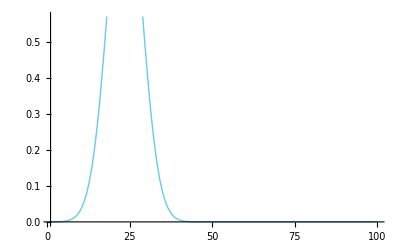

```mathematica
Plot[gaun[n,fs[list0[[2]]],ax/.maxi[list0[[2]]][[2]]][ax],{ax,1,100}]
```

```mathematica
ClearAll[con];con[f_]:=con[f]=1/NIntegrate[ddir[ax,n,f],{ax,0,10^6}]
```

```mathematica
ClearAll[nddir];nddir[aa_,nx_,f_]:=ddir[aa,nx,f]*con[f]
```

```mathematica
list0=FoldList[Join,{6},T@{{57,32,66,75,88,93,22,14,21,43,89,70,90}}]
```

{{6},{6,57},{6,57,32},{6,57,32,66},{6,57,32,66,75},{6,57,32,66,75,88},{6,57,32,66,75,88,93},{6,57,32,66,75,88,93,22},{6,57,32,66,75,88,93,22,14},{6,57,32,66,75,88,93,22,14,21},{6,57,32,66,75,88,93,22,14,21,43},{6,57,32,66,75,88,93,22,14,21,43,89},{6,57,32,66,75,88,93,22,14,21,43,89,70},{6,57,32,66,75,88,93,22,14,21,43,89,70,90}}

```mathematica
listsample:=Block[{rsam=RandomSample[Range[94],Length@Last[list0]]},FoldList[Join,{rsam[[1]]},T@{rsam[[2;;]]}]]
```

```mathematica
listsample0=listsample;
```

```mathematica
maxi[k_]:=maxi[k]=NMaximize[{Log@ddir[ax,n,fs[k]],1<ax<10^5},ax];
```

```mathematica
gtabcomp=Table[
maxt=maxi[k];
maxp=Exp@maxt[[1]];maxa=(ax/.maxt[[2]]);
std=10/Sqrt@Abs@lddir2[maxa,n,fs[k]];
gauf[ax_]=gaun[n,fs[k],maxa][ax];
Plot[{ddir[ax,n,fs[k]]/maxp,gauf[ax]},{ax,Max[maxa-std,0],maxa+std},PlotRange->{0,1},Frame->Auto,Axes->None,FrameStyle->Directive[Black,Bold,18],
PlotLegends->Auto,FrameLabel->{{p[A | Length[k]],None},{A,None}}],{k,list0[[1;;11]]}];
```

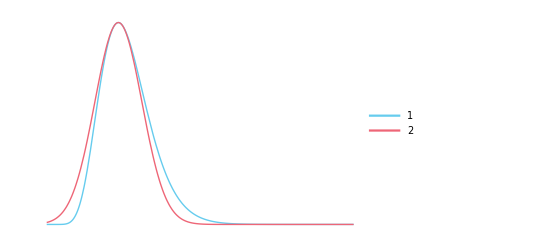
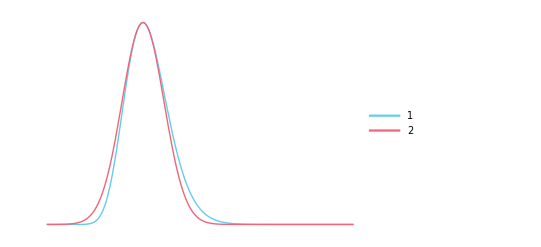
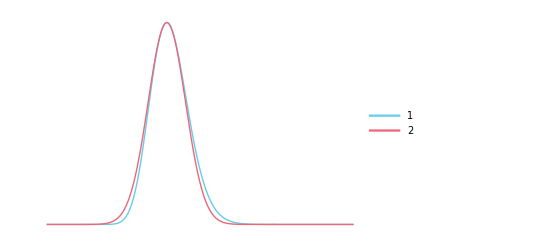
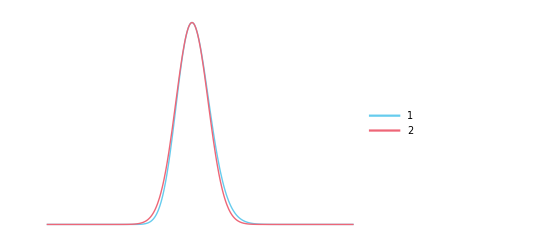
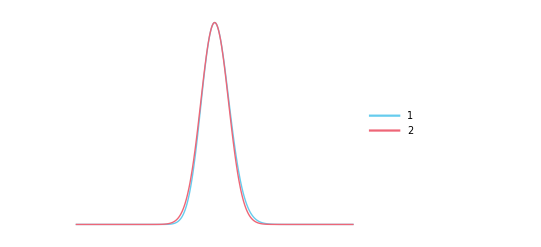
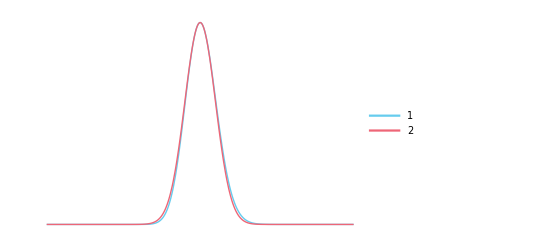
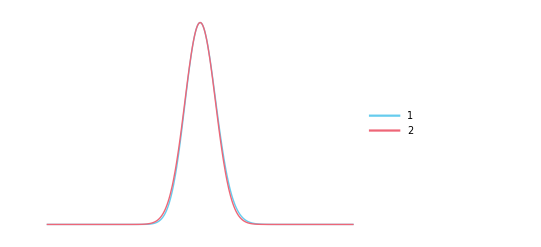
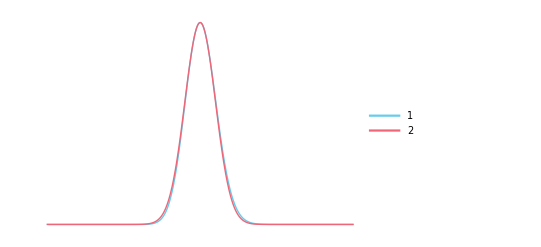
(-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-)

```mathematica
gtabcomp//MF
```

```mathematica
fr=fs[list0[[1]]];tx=Length[fr];
maxa=(ax/.maxi[list0[[1]]][[2]]);fun[ax_]=FS[ddir[ax,n,fr]/maxa];
af=NIntegrate[(n*fr+aa/tx)/(n+aa)*fun[aa],{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2];
af=af/Total[af]
```

{0.249253,0.152257,0.0403888,0.0255171,0.113921,0.0686449,0.0448503,0.0288219,0.0669925,0.037084,0.00833214,0.00420113,0.0461722,0.0250214,0.0545994,0.0339444}

```mathematica
mf=(n*fr+maxa/tx)/(n+maxa)
```

{0.249327,0.152292,0.04038,0.0255024,0.113941,0.0686473,0.0448432,0.0288085,0.0669943,0.0370738,0.00831056,0.00417791,0.0461657,0.0250065,0.0545963,0.033933}

```mathematica
cf=(n*fr+tx/2/tx)/(n+tx/2)
```

{3015/12074,1841/12074,487/12074,307/12074,1377/12074,829/12074,541/12074,347/12074,809/12074,447/12074,99/12074,49/12074,557/12074,301/12074,659/12074,409/12074}

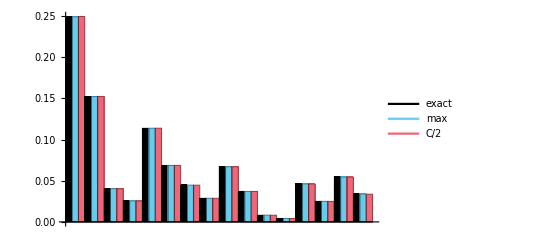

```mathematica
BarChart[T@{af,mf,cf},ChartLayout->"Grouped",ChartStyle->{Black,blue,red},ChartLegends->mylegendsc[{Black,blue,red},{"exact","max","C/2"},Bottom]]
```

```mathematica
expdf["comparefinalfreqs_1",%]
```

comparefinalfreqs_1.pdf

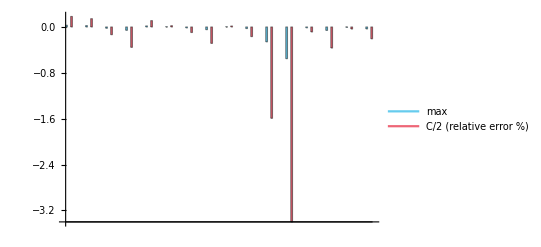

```mathematica
BarChart[T@{mf-af,cf-af}/af*100,ChartLayout->"Grouped",ChartStyle->{blue,red},ChartLegends->mylegendsc[{blue,red},{"max","C/2    (relative error %)"},Bottom]]
```

```mathematica
expdf["comparefinalfreqs_diff_1",%]
```

comparefinalfreqs_diff_1.pdf

```mathematica
Precision
```

```mathematica
gtab=Table[
maxt=maxi[k];
maxp=Exp@maxt[[1]];maxa=(ax/.maxt[[2]]);

Plot[ddir[ax,n,fs[k]]/maxp,{ax,Max[maxa-100,0],maxa+100},PlotRange->{0,1},Frame->Auto,Axes->None,FrameStyle->Directive[Black,Bold,18],
PlotLegends->Auto,FrameLabel->{{p[A | Length[k]],None},{A,None}}],{k,list0}];
```

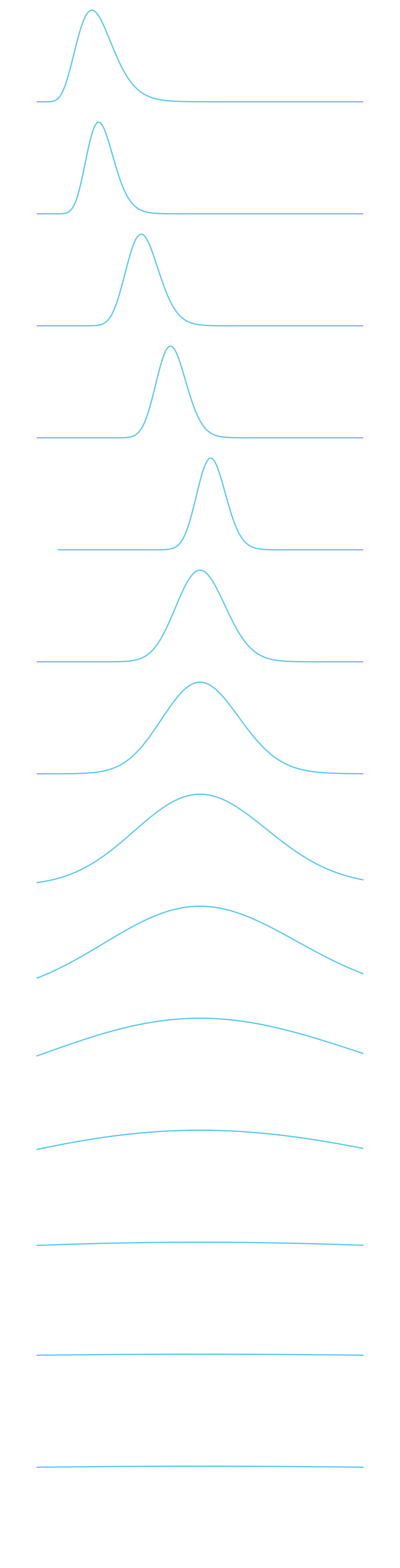
(-Graphics-)

```mathematica
gtab//MF
```